```mathematica
<<AceFEM`;
<<AceGen`;
MaxNodes=25;
acemode={"Plain","Prototype","Debug","Optimal"}[[4]];
SeedRandom[1];
```

Accompanying code for article:  Bode, T. (2023): One-point quadrature of higher-order finite and virtual elements in nonlinear analysis. Computational mechanics.

DOI: https://doi.org/10.1007/s00466-023-02406-8

All equation references in the commentation refer to the numbering in the article.

GNU GENERAL PUBLIC LICENSE Version 3, 29 June 2007

Version 1, 27.10.2023

## Element generation

### Second order VEM serendipity polygon definition for momentum equation, moment integration

#### Function definitions

```mathematica
triangles=False;
fullMomentOrder=True;
om=1;
ox=4;
mOrder=Max[4,ox];

"Reading input data for element routines";
GeneralDefinitions[]:=(
ndim=SMSNoDimensions;
nNoDOFs=SMSDOFGlobal⟦1⟧;

If[triangles,
MaxNodes=6;
nNodes=MaxNodes;
nDOF=MaxNodes ndim;
,
nNodes⊢SMSLastTrueNode[];
nDOF⊢nNodes ndim;
];

Δt⊨SMSReal[rdata$$["TimeIncrement"]];
SMSArray[XI,nDOF,Function[{dof},SMSReal[nd$$[SMSInteger[(dof-1)/ndim+1],"X",SMSMod[dof-1,ndim]+1]]]];
SMSArray[uI,nDOF,Function[{dof},SMSReal[nd$$[SMSInteger[(dof-1)/ndim+1],"at",SMSMod[dof-1,ndim]+1]]]];
Em⊨SMSIO["Domain data","E"->{"E -Youngs modulus",{210000,210000},True}];
ν⊨SMSIO["Domain data","ν"->{"ν -Poisson ratio",{0.3,0.3},True}];
{λ,μ}⊨SMSHookeToLame[Em,ν];
);

"Element contribution is assembled in node data";
ResidualInNodeData[offset_]:=(
SMSArray[Rg,nDOF,Function[{dof},SMSD[potential,uI,dof,"Method"->"Backward"]]];

SMSDo[l,1,nNodes];
	SMSDo[d,1,ndim];
		SMSExport[SMSPart[Rg,(l-1)ndim+d],nd$$[l,"Data",offset+d],"AddIn"->True,"Atomic"->True];
	SMSEndDo[];
SMSEndDo[];
);

SurfaceIntegral[]:=("Part of eq. (56)";
"Normal for middle node";
nS⊨Table[SMSPart[nI,(SMSInteger[II/2]-1) ndim+d],{d,ndim}];
"Adjacent normals of vertex node";
nl⊨Table[SMSPart[nI,(SMSInteger[SMSMod[nNodes+(II-1)/2-1,nNodes/2]+1]-1) ndim+d],{d,ndim}];
nr⊨Table[SMSPart[nI,(SMSInteger[(II+1)/2]-1) ndim+d],{d,ndim}];
"Gauß-Lobatto";
tmp⊨SMSIf[SMSMod[II,2]==0,2/3 nS,1/6( nl+ nr)];
{xII,yII}⊨Table[SMSPart[XI,(II-1) ndim+d],{d,ndim}]-Xc;
"n_o^e.ϵ_(π, SubscriptBox[a, SubscriptBox[ϵ, π]])";
stmp⊨tmp.SMSReplaceAll[cπ,{Χ[[1]]->xII,Χ[[2]]->yII}];

stmp
);

SurfaceIntegralAsym[]:=(
"Same procedure as in SurfaceIntegral[]";
nS⊨Table[SMSPart[nI,(SMSInteger[II/2]-1) ndim+d],{d,ndim}];
nl⊨Table[SMSPart[nI,(SMSInteger[SMSMod[nNodes+(II-1)/2-1,nNodes/2]+1]-1) ndim+d],{d,ndim}];
nr⊨Table[SMSPart[nI,(SMSInteger[(II+1)/2]-1) ndim+d],{d,ndim}];
tmp⊨SMSIf[SMSMod[II,2]==0,2/3 nS,1/6( nl+ nr)];
{xII,yII}⊨Table[SMSPart[XI,(II-1) ndim+d],{d,ndim}]-Xc;

tmp
);

ResidualAndTangent[]:=("Eq. 28";
SMSDo[l,1,nDOF];
	Rg⊨SMSD[potential,uI,l,"Method"->"Backward"];
	SMSExport[Rg,p$$[l],"AddIn"->True];
	SMSDo[m,If[SMSSymmetricTangent,l,1],nDOF];
		Kg⊨SMSD[Rg,uI,m,"Method"-> "Backward"];
		SMSExport[ Kg,s$$[l,m],"AddIn"->True];
	SMSEndDo[];
SMSEndDo[];
);

GetMoments[]:=(
"Load moments from element data and write them into M_i";
MFlat=Table[SMSReal[ed$$["Data",2+a]],{a,Sum[i,{i,mOrder+1}]}];
Subscript[M, 0]⊨MFlat⟦1⟧;
pBismOrder=Flatten[Table[Table[x^(j-i)y^i,{i,0,j}],{j,0,mOrder}]];
Do[
ms={x,y};
Do[ms=ms⊗{x,y};,{j,i-1}];
pos=Flatten[Position[pBismOrder,#,1]&/@(ms//Flatten)];
ms=MFlat[[pos]];
Do[ms=Partition[ms,ndim],{j,i-1}];
Subscript[M, i]⊨ms;
,{i,1,mOrder}];

"Load centroid";
	Xc⊨Table[SMSReal[ed$$["Data",a]],{a,2}];
);

GetProjection[]:=(
If[triangles,
"T2-FEM (via least squares)";
XI0⊨Table[Table[SMSReal[nd$$[i,"X",j]],{j,ndim}],{i,6}];
Xc0⊨(XI0⟦1⟧+XI0⟦3⟧+XI0⟦5⟧)/3;
XI6⊨Table[Table[SMSReal[nd$$[i,"X",j]],{j,ndim}]-Xc0,{i,6}];
uIx⊨Table[SMSReal[nd$$[i,"at",1]],{i,6}];
pI⊨({1,#⟦1⟧,#⟦2⟧,(#⟦1⟧)^2,(#⟦2⟧)^2,#⟦1⟧ #⟦2⟧}&/@XI6);
a⊨SMSLinearSolve[pIᵀ.pI,pIᵀ.uIx,"Symmetric"->True];
SMSFreeze[Χ,Table[0,{j,ndim}]];
ux⊨a.{1,Χ⟦1⟧,Χ⟦2⟧,Χ⟦1⟧^2,Χ⟦2⟧^2,Χ⟦1⟧ Χ⟦2⟧};
NI⊨SMSD[ux,uIx];
uI6⊨Table[SMSPart[uI,(i-1) ndim+d],{i,6},{d,ndim}];
uπ⊨NI.uI6;
,
	"Eq. (51) ,cumbersome implementation via Taylor expansion in order to ensure symmetries of higher order derivatives for moment integration";
utmp⫤Table[0,{j1,ndim}];
Htmp⫤Table[0,{j1,ndim},{j2,ndim}];
dHtmp⫤Table[0,{j1,ndim},{j2,ndim},{j3,ndim}];
SMSFreeze[Χtmp,Table[0,{j,ndim}]];
SMSDo[nod,1,nNodes,1,{utmp,Htmp,dHtmp}];
	ui⊨Table[SMSPart[uI,(nod-1) ndim+d],{d,ndim}];
	Ni11⊨Table[SMSReal[ed$$["Data",2+Sum[i,{i,mOrder+1}]+24(nod-1)+d]],{d,6}].{1,Χtmp⟦1⟧,Χtmp⟦2⟧,Χtmp⟦1⟧^2,Χtmp⟦1⟧ Χtmp⟦2⟧,Χtmp⟦2⟧^2};
	Ni21⊨Table[SMSReal[ed$$["Data",2+Sum[i,{i,mOrder+1}]+24(nod-1)+6+d]],{d,6}].{1,Χtmp⟦1⟧,Χtmp⟦2⟧,Χtmp⟦1⟧^2,Χtmp⟦1⟧ Χtmp⟦2⟧,Χtmp⟦2⟧^2};
	Ni12⊨Table[SMSReal[ed$$["Data",2+Sum[i,{i,mOrder+1}]+24(nod-1)+12+d]],{d,6}].{1,Χtmp⟦1⟧,Χtmp⟦2⟧,Χtmp⟦1⟧^2,Χtmp⟦1⟧ Χtmp⟦2⟧,Χtmp⟦2⟧^2};
	Ni22⊨Table[SMSReal[ed$$["Data",2+Sum[i,{i,mOrder+1}]+24(nod-1)+18+d]],{d,6}].{1,Χtmp⟦1⟧,Χtmp⟦2⟧,Χtmp⟦1⟧^2,Χtmp⟦1⟧ Χtmp⟦2⟧,Χtmp⟦2⟧^2};
	Ni⊨{{Ni11,Ni12},{Ni21,Ni22}};
	dNi⊨SMSD[Ni,Χtmp];
	ddNi⊨SMSD[dNi,Χtmp];
	utmp⊣utmp+Ni.ui;
	Htmp⊣Htmp+Table[Sum[dNi[[a,d,b]]ui[[d]],{d,ndim}],{a,ndim},{b,ndim}];
dHtmp⊣dHtmp+Table[Sum[ddNi[[a,d,b,c]]ui[[d]],{d,ndim}],{a,ndim},{b,ndim},{c,ndim}];
SMSEndDo[{utmp,Htmp,dHtmp}];
SMSFreeze[Χ,Table[0,{j,ndim}]];
uπ⊨utmp+Table[Sum[Htmp[[a,b]]Χ[[b]],{b,ndim}],{a,ndim}]+1/2 Table[Sum[dHtmp[[a,b,c]]Χ[[b]]Χ[[c]],{b,ndim},{c,ndim}],{a,ndim}];
];
);

Kinematics[]:=(
Hπ⊨SMSD[uπ,Χ,"Ignore"->NumberQ];
dHπ⊨SMSD[Hπ,Χ,"Ignore"->NumberQ];
SMSFreeze[F,IdentityMatrix[3]+{{Hπ⟦1,1⟧,Hπ⟦1,2⟧,0},{Hπ⟦2,1⟧,Hπ⟦2,2⟧,0},{0,0,0}}];
SMSFreeze[CC,Fᵀ.F,"Symmetric"->True];
JC⊨SMSDet[CC];
);

"Integration of strain energy over element";
If[!fullMomentOrder,
"Integration split";
Integration[C_]:=(
ox=mOrder;
Ψ=W;

"Material nonlinearity om";
Subscript[ΨdC, 1]⊨SMSD[Ψ,SMSVariables[C]];
Do[Subscript[ΨdC, m]⊨SMSD[SMSVariables[Subscript[ΨdC, m-1]],SMSVariables[C]];,{m,2,om+1}];
Subscript[ΨdC, om+2]⊨Table[0,{Length[SMSVariables[Subscript[ΨdC, om+1]]]},{Length[SMSVariables[C]]}] ;

"Spatial derivatives";
Subscript[ΨdX, 1]⊨SMSD[Ψ,Χ,"Dependency"->{{Ψ,SMSVariables[C],Subscript[ΨdC, 1]}}];
Do[Subscript[ΨdX, x]⊨SMSD[Subscript[ΨdX, x-1],Χ,"Dependency"->Table[{SMSVariables[Subscript[ΨdC, m]],SMSVariables[C],Subscript[ΨdC, m+1]},{m,1,Min[om,x-1]}]];,{x,2,ox}];

"Moment integration up to order ox";
Ππ⊨Subscript[M, 0] Ψ+Sum[1/(i!)Flatten[Subscript[M, i]].Flatten[Subscript[ΨdX, i]],{i,1,ox}];);
,
"Full material nonlinearities considered in derivatives (advised if derivatives are available)";
Integration[CC_]:=(
Ψ=W;
	Subscript[ΨdX, 1]⊨SMSD[W,Χ,"Ignore"->NumberQ];
	Do[Subscript[ΨdX, x]⊨SMSD[Subscript[ΨdX, x-1],Χ];,{x,2,ox}];
	Ππ⊨Subscript[M, 0] Ψ+Sum[1/(i!)Flatten[Subscript[M, i]].Flatten[Subscript[ΨdX, i]],{i,1,ox}];
);];

Stabilization[CC_]:=("Eq. (26,27)";
"Material tangent and stabilization coefficient";
ℂ⊨SMSD[SMSD[W,CC,"Ignore"->NumberQ,"Symmetric"->True],CC,"Ignore"->NumberQ,"Symmetric"->True];
βs⊨SMSIO["Domain data","βs"->{"βs -Stabilization parameter",{0.5,0.5},True}];
γ⊨βs 1/2 Sum[ℂ[[a,b,c,d]] 1/2(KroneckerDelta[a,c]KroneckerDelta[b,d]+KroneckerDelta[a,d] KroneckerDelta[b,c]),{a,ndim},{b,ndim},{c,ndim},{d,ndim}];
"Loop over all vertices";
Πs⫤0;
SMSDo[i,1,nNodes,1,Πs];
	ui⊨Table[SMSPart[uI,(i-1) ndim+d],{d,ndim}];
	Xi⊨Table[SMSPart[XI,(i-1) ndim+d],{d,ndim}];
	ΔXi⊨Xi-Xc;
	"Projection evaluated at node i";
	uπi⊨uπ+Hπ.ΔXi+1/2 Table[Sum[dHπ[[a,b,c]]ΔXi[[b]]ΔXi[[c]],{b,ndim},{c,ndim}],{a,ndim}];
	"Right part of eq. (23)";
	ΔuI⊨ui-uπi;
	Πs⊣Πs+γ/2 ΔuI.ΔuI;
SMSEndDo[Πs];
);

VolumeLoads[]:=("Internal volume load if considered as in eq. (64)";
"Taylor expansion of volume load, coefficients from element data";
ρ0b⊨SMSReal[rdata$$["Multiplier"]] Table[Table[SMSReal[ed$$["Data",2+Sum[i,{i,mOrder+1}]+24*MaxNodes+6(d-1)+a]],{a,6}].{1,Χ⟦1⟧,Χ⟦2⟧,Χ⟦1⟧^2,Χ⟦1⟧ Χ⟦2⟧,Χ⟦2⟧^2},{d,ndim}];
SMSIf[ρ0b.ρ0b<10^-8];
	Πρ0b⫤0;
SMSElse[];
	"Volume load potential with spatial derivatives";
	Wb⊨ρ0b.uπ;
	WbX1⊨SMSD[Wb,Χ];
	WbX2⊨SMSD[WbX1,Χ];
	WbX3⊨SMSD[WbX2,Χ];
	WbX4⊨SMSD[WbX3,Χ];
		
	"Moment integration of volume load potential";Πρ0b⊣(Subscript[M, 0] Wb+WbX1.Subscript[M, 1]+1/2 Tr[Subscript[M, 2].WbX2ᵀ]+1/6 Sum[Subscript[M, 3]⟦a,b,c⟧WbX3⟦a,b,c⟧,{a,ndim},{b,ndim},{c,ndim}]+1/24 Sum[Subscript[M, 4]⟦a,b,c,d⟧WbX4⟦a,b,c,d⟧,{a,ndim},{b,ndim},{c,ndim},{d,ndim}]);
SMSEndIf[Πρ0b];
);
```

#### Initialization

```mathematica
nDIM=2;
SMSInitialize["VEM2-NH-"<>If[fullMomentOrder,"MF","M"<>ToString[om]]<>"-X"<>ToString[ox],"Environment"->"AceFEM","Mode"->acemode];
SMSTemplate["SMSTopology"->("V"<>ToString[nDIM]),
"SMSCharSwitch"->{"Initialization","GetNormals","ClearNormals"},
"SMSNoNodes" -> MaxNodes,
"SMSDOFGlobal"->nDIM,
"SMSNodeID"->Table["D -D",{MaxNodes}],
"SMSAdditionalNodes"->Null,
"SMSSymmetricTangent"->True,
"SMSDomainDataNames"->{"E -elastic modulus","ν -poisson ratio","βs -Stabilization paramter"},
"SMSDefaultData"->{210000,0.3,0.5},
"SMSNoElementData"->2+Sum[i,{i,mOrder+1}]+24*MaxNodes+2 6+2 6(*Storage: centroid(2) + moments (1+2+3+4+5) + shape functions + source term + analytic solution (for calculation of error norms)*),
"SMSNoNodeData"->2 nDIM];
```

#### Tasks

```mathematica
"3 Tasks, evaluated in preprocessing:
1 -> Calculate moments (eq. 13) and L2 projection of shape functions (eq. 62, sec. 3.2)
2 -> Compute nodal load applicants for surface and volume loads (sec. 3.4)";
```

```mathematica
SMSStandardModule["Tasks"];
GeneralDefinitions[];
task⊢SMSInteger[Task$$];
SMSIf[task<0,
SMSSwitch[task
,-1,
SMSIO[{1,0,0,0,0}, "Export to","Task data"];SMSReturn[];
,-2,
SMSIO[{1,0,0,0,0}, "Export to","Task data"];SMSReturn[];
,-3,
SMSIO[{1,0,0,0,0}, "Export to","Task data"];SMSReturn[];
];];
```

Task for calculation of projected shape functions (executed in preprocessing)

```mathematica
SMSIf[task==1];

"Normals of edges considering sequential numbering of nodes";
SMSArray[nI,nNodes,Function[{dof},
II⊨SMSInteger[(dof-1)/ndim+1];
{x1,y1}⊨Table[SMSPart[XI,(2II-2) ndim+d],{d,ndim}];
{x2,y2}⊨Table[SMSPart[XI,(SMSMod[2II,nNodes]) ndim+d],{d,ndim}];
n⊨{-y1+y2,x1-x2};
SMSPart[n,SMSMod[dof-1,ndim]+1]
]];

"Projection basis and derivatives";
pT={1,x,y,x^2,x y,y^2};
p={x,y,x^2,x y,y^2};
dpdx={D[p,{x,1}],D[p,{y,1}]}ᵀ;
Δp=D[p,{x,2}]+D[p,{y,2}];

"Loop eq. (63) over all edges, Calculation and storage of element centroid using 0th and first order moments";
MpT⫤Table[0,{i,Length[pT]}];
SMSDo[II,1,nNodes/2,1,MpT];
	"x component of normal of edge II";
	nx⊨SMSPart[nI,(II-1) ndim+1]; 
	"coordinate of first vertex";
	{x1,y1}⊨Table[SMSPart[XI,(2II-2) ndim+d],{d,ndim}];
	"coordinate of second vertex";
	{x2,y2}⊨Table[SMSPart[XI,SMSInteger[(SMSMod[2II,nNodes]) ndim+d]],{d,ndim}];
	"Line integral";
	MpT⊣MpT+Factor@Integrate[nx (Integrate[pT,x]/.x->x1+s (x2-x1)/.y->y1+s (y2-y1)),{s,0,1}];
SMSEndDo[MpT];
Xc⊨MpT[[{2,3}]]/MpT[[1]];
SMSExport[Xc,Table[ed$$["Data",d],{d,2}],"AddIn"->False];

"Recompute moments with respect to centroid, eq. (63)";
MpT⫤Table[0,{i,Length[pT]}];
SMSDo[II,1,nNodes/2,1,MpT];
	nx⊨SMSPart[nI,(II-1) ndim+1]; 
	{x1,y1}⊨Table[SMSPart[XI,(2II-2) ndim+d],{d,ndim}]-Xc;(*<-with respect to centroid*)
	{x2,y2}⊨Table[SMSPart[XI,SMSInteger[(SMSMod[2II,nNodes]) ndim+d]],{d,ndim}]-Xc;
	MpT⊣MpT+Factor@Integrate[nx (Integrate[pT,x]/.x->x1+s (x2-x1)/.y->y1+s (y2-y1)),{s,0,1}];
SMSEndDo[MpT];
SMSFreeze[Subscript[M, 0],MpT[[1]],"Dependency"->True];
SMSFreeze[Subscript[M, 1],{MpT[[2]],MpT[[3]]},"Dependency"->True];
SMSFreeze[Subscript[M, 2],{{MpT[[4]],MpT[[5]]},{MpT[[5]],MpT[[6]]}},"Dependency"->True,"Symmetric"->True];

"Computation and storage of moments for integration of weak form (complete up to fourth order, eq. (63))";
MpBismOrder⫤Table[0,{i,Sum[i,{i,mOrder+1}]}];
SMSDo[II,1,nNodes/2,1,MpBismOrder];
	nx⊨SMSPart[nI,(II-1) ndim+1]; 
	{x1,y1}⊨Table[SMSPart[XI,(2II-2) ndim+d],{d,ndim}]-Xc;
	{x2,y2}⊨Table[SMSPart[XI,SMSInteger[(SMSMod[2II,nNodes]) ndim+d]],{d,ndim}]-Xc;
	pBismOrder=Flatten[Table[Table[x^(j-i)y^i,{i,0,j}],{j,0,mOrder}]];
	MpBismOrder⊣MpBismOrder+Factor@Integrate[nx (Integrate[pBismOrder,x]/.x->x1+s (x2-x1)/.y->y1+s (y2-y1)),{s,0,1}];
SMSEndDo[MpBismOrder];
SMSExport[MpBismOrder,Table[ed$$["Data",2+d],{d,Sum[i,{i,mOrder+1}]}],"AddIn"->False];

"Eq. (48), Serendipity projection (least square collocation)";
"Mass matrix/moment matrix/shape tensor is assembled";
MpI⫤Table[0,{i,Length[pT]},{i,Length[pT]}];
SMSDo[i,1,nNodes,1,MpI];
	{xi,yi}⊨Table[SMSPart[XI,(i-1) ndim+d],{d,ndim}]-Xc;
	pTi⊨(pT/.x->xi/.y->yi);
	MpI⊣MpI+pTi⊗pTi;
SMSEndDo[MpI];
"Inverse of mass matrix (Right part of second line of eq. (48))";
MpIi⊨SMSLinearSolve[MpI,IdentityMatrix[MpI//Length]];
"Right hand side, left part of second line of eq. (48)";
acTmp⫤Table[0,{ndim},{Length[pT]}];
SMSDo[II,1,nNodes,1,acTmp];
	{xI,yI}⊨Table[SMSPart[XI,(II-1) ndim+d],{d,ndim}]-Xc;
	ui⊨Table[SMSPart[uI,(II-1) ndim+d],{d,ndim}];
	acTmp⊣acTmp+ui⊗(pT/.x->xI/.y->yI);
SMSEndDo[acTmp];
"Eq. (46,47), Compute coefficents and approximation of virtual moment";
ac⊨acTmp.MpIi;
m0⊨ac.MpT;

"Eq. (52,53), L2 projection of strain";
"9 coefficients (pa): 3 components * linear approximation (3)";
SMSFreeze[pa,Table[SMSFictive[],{i,9}]];
Χ⊨Table[SMSFictive[],{d,ndim}];
pϵ⊨{1,Χ[[1]],Χ[[2]]};
ϵπF⊨Partition[pa,3].pϵ;
ϵπ⊨{ϵπF[[{1,3}]],ϵπF[[{3,2}]]};
ϵπpa⊨SMSD[ϵπ,pa];
"Eq. (55), Moment integration projection part";
int1⊨Table[Sum[ϵπ[[a,b]] ϵπpa[[a,b,i]],{a,ndim},{b,ndim}],{i,Length[pa]}];
int1x1⊨SMSD[int1,Χ];
int1x2⊨SMSD[int1x1,Χ];
Qϵπ⊨Subscript[M, 0] int1+Table[Sum[int1x1[[i,d1]]Subscript[M, 1][[d1]],{d1,ndim}],{i,Length[pa]}]+(1/2)Table[Sum[int1x2[[i,d1,d2]]Subscript[M, 2][[d1,d2]],{d1,ndim},{d2,ndim}],{i,Length[pa]}];
```

```mathematica
"Eq. (56), surface integral of virtual shape functions";
"cπ=ϵ_(π, SubscriptBox[a, SubscriptBox[ϵ, π]])";
cπ=SMSD[ϵπ,pa];
"Grad[ϵ_(π, SubscriptBox[a, SubscriptBox[ϵ, π]])]";
dcπdx⊨SMSD[cπ,Χ];
"Div[ϵ_(π, SubscriptBox[a, SubscriptBox[ϵ, π]])]";
Divdcda⊨Table[Sum[dcπdx[[a,d,i,d]],{d,ndim}],{a,ndim},{i,Length[pa]}];
"Assembling left part of last line of eq. (56)";
sInt⫤Table[0,{i,Length[pa]}];
SMSDo[II,1,nNodes,1,sInt];
	{xI,yI}⊨Table[SMSPart[XI,(II-1) ndim+d],{d,ndim}]-Xc;
	ui⊨Table[SMSPart[uI,(II-1) ndim+d],{d,ndim}];
	"Surface integral is evaluated via Gauß-Lobatto where vertex nodes are summed up";
	"∫(u_h⊗n_o^e):ϵ_(π, SubscriptBox[a, SubscriptBox[ϵ, π]])dΩ^e, see function SurfaceIntegral[]";
	sInt⊣sInt+ui.SurfaceIntegral[];
SMSEndDo[sInt];
"add right part of eq. (56) to surface integral";
Qϵ⊨sInt-m0.Divdcda;
```

```mathematica
"Eq. (54), solve for coefficients with one Newton step";
Qp⊨Flatten[Qϵπ-Qϵ];
Qp0⊨SMSReplaceAll[Qp,Flatten[{{Χ[[1]]->0,Χ[[2]]->0},Table[pa[[i]]->0,{i,Length[pa]}]}]];
Kp⊨SMSD[Qp,pa];
Kp0⊨SMSReplaceAll[Kp,{Χ[[1]]->0,Χ[[2]]->0}];
Kpi⊨SMSLinearSolve[Kp0,IdentityMatrix[Kp0//Length]];
aπϵ⊨-Kpi.Qp0;

"Eq. (52), Projected strain and derivative";
ϵπTF⊨Partition[aπϵ,3].pϵ;
ϵπT⊨{ϵπTF[[{1,3}]],ϵπTF[[{3,2}]]};
dϵπT⊨SMSD[ϵπT,Χ];

"Eq. (61), L2 projection of anti-symmetric part, constant ansatz, same procedure as with strain";
sInt2⫤0;
SMSDo[II,1,nNodes,1,sInt2];
	{xI,yI}⊨Table[SMSPart[XI,(II-1) ndim+d],{d,ndim}]-Xc;
	ui⊨Table[SMSPart[uI,(II-1) ndim+d],{d,ndim}];
	sInt2⊣sInt2+(1/2){-ui[[2]],ui[[1]]}.SurfaceIntegralAsym[];
SMSEndDo[sInt2];
ϵπas⊨sInt2/MpT[[1]];

"Comparing coefficients of second order projection of displacement field with eq. (58-61)";
"Projected displacement field";
pu⊨{1,Χ[[1]],Χ[[2]],Χ[[1]]^2,Χ[[1]] Χ[[2]],Χ[[2]]^2};
aπf⊨Table[SMSFictive[],{d,ndim},{Length[pu]}];
uπf⊨aπf.pu;
"Symmetric (linear) and antisymmetric (constant) parts";
Huπf⊨SMSD[uπf,Χ];
ϵπf⊨(1/2)(Huπf+Huπfᵀ);
ϵπasf⊨(1/2)(Huπf-Huπfᵀ);
dϵuπf⊨SMSD[ϵπf,Χ];
"Eq. (58)";
QNϵsym⊨Flatten[ϵπf-ϵπT];
"Eq. (61)";
QNϵasym⊨ϵπasf[[1,2]]-ϵπas;
"Eq. (59)";
QNdϵ⊨dϵuπf-dϵπT;
"Eq. (60)";
QN0⊨aπf.MpT[[;;6]]-m0;
"Get coefficients with one Newton step";
QN⊨Flatten[{QN0,SMSVariables[QNϵsym],QNϵasym,SMSVariables[QNdϵ]}];
QN00⊨SMSReplaceAll[QN,Flatten[{{Χ[[1]]->0,Χ[[2]]->0},Table[aπf[[i,j]]->0,{i,ndim},{j,Length[pu]}]}]];
KN⊨SMSD[QN,Flatten[aπf]];
KN0⊨SMSReplaceAll[KN,{Χ[[1]]->0,Χ[[2]]->0}];
KNi⊨SMSInverse[KN0];
aπall⊨-KNi.QN00;
```

```mathematica
"Export polynomial shape functions coefficients (NIπ=aπI.p)";
SMSDo[II,1,nNodes ndim];
	"Coefficients of eq. (62)";
	aπI⊨SMSD[aπall,uI,II];
SMSExport[aπI,Table[ed$$["Data",2+Sum[i,{i,mOrder+1}]+12(II-1)+d],{d,12}],"AddIn"->False];
SMSEndDo[];
SMSEndIf[];
```

Clear node data for assembly of effective nodal normals and volume load applicants

```mathematica
SMSIf[task==3,

SMSDo[II,1,nNodes];
	SMSExport[Table[0,{d,2ndim}],Table[nd$$[II,"Data",d],{d,2ndim}],"AddIn"->False];
SMSEndDo[];
];
```

Element contribution for effective nodal normals and volume load applicants

```mathematica
SMSIf[task==2,
"Calculation of effective nodal normals";
GeneralDefinitions[];
GetMoments[];
GetProjection[];
Kinematics[];

"eq. (65)";
W⊨Tr[F];

"Derivatives for moment integration";
dWdX⊨SMSD[W,Χ];
dWdX2⊨SMSD[dWdX,Χ];
dWdX3⊨SMSD[dWdX2,Χ];
dWdX4⊨SMSD[dWdX3,Χ];

	"Moment integration";
Ππ⊨Subscript[M, 0] W+Sum[Subscript[M, 1]⟦a⟧dWdX⟦a⟧,{a,ndim}]+1/2 Sum[Subscript[M, 2]⟦a,b⟧dWdX2⟦a,b⟧,{a,ndim},{b,ndim}]+1/6 Sum[Subscript[M, 3]⟦a,b,c⟧dWdX3⟦a,b,c⟧,{a,ndim},{b,ndim},{c,ndim}]+1/24 Sum[Subscript[M, 4]⟦a,b,c,d⟧dWdX4⟦a,b,c,d⟧,{a,ndim},{b,ndim},{c,ndim},{d,ndim}];


"eq. (66), Assemble global residual in node data";
potential=Ππ;
ResidualInNodeData[0];


"eq. (67), Calculation nodal volume load constants";
ϵ⊨1/2(Hπ+Hπᵀ);
W⊨1/2 Tr[ϵ.ϵᵀ];

"Derivatives for moment integration";
dWdX⊨SMSD[W,Χ];
dWdX2⊨SMSD[dWdX,Χ];
dWdX3⊨SMSD[dWdX2,Χ];
dWdX4⊨SMSD[dWdX3,Χ];

"Moment integration";
Ππ⊨Subscript[M, 0] W+Sum[Subscript[M, 1]⟦a⟧dWdX⟦a⟧,{a,ndim}]+1/2 Sum[Subscript[M, 2]⟦a,b⟧dWdX2⟦a,b⟧,{a,ndim},{b,ndim}]+1/6 Sum[Subscript[M, 3]⟦a,b,c⟧dWdX3⟦a,b,c⟧,{a,ndim},{b,ndim},{c,ndim}]+1/24 Sum[Subscript[M, 4]⟦a,b,c,d⟧dWdX4⟦a,b,c,d⟧,{a,ndim},{b,ndim},{c,ndim},{d,ndim}];

"eq. (69), Assemble global residual in node data";
potential=Ππ;
ResidualInNodeData[2];
];
```

#### Residual and tangent

```mathematica
SMSStandardModule["Tangent and residual"];
"Initalization, load moments";
GeneralDefinitions[];
GetMoments[];

"Compute Projection using projected shape functi";
GetProjection[];
Kinematics[];
VolumeLoads[];
```

```mathematica
"Select strain energy function";
Switch[1
,1,"neo-Hooke";
W⊨μ/2(Tr[CC]-3-2Log[SMSSqrt[JC]])+λ/4( SMSSqrt[JC]^2-1-2Log[SMSSqrt[JC]]);
"Integrate strain energy using moment integration";
Integration[CC];
"Compute stabilization potential";
Stabilization[CC];

,2,"St. Venant";
SMSFreeze[𝔼,1/2(CC-IdentityMatrix[3]),"Symmetric"->True];
W⊨μ(Tr[𝔼.𝔼]+ν Tr[𝔼]^2/(1-2ν));
Integration[CC];
Stabilization[CC];

,3,"linear elastic, small deformations";
SMSFreeze[ϵ,1/2(Hπᵀ+Hπ),"Symmetric"->True];
W⊨μ(Tr[ϵ.ϵ]+ν Tr[ϵ]^2/(1-2ν));
Integration[ϵ];
Stabilization[ϵ];
];
```

```mathematica
"Eq. (28), Tangent and residual";
potential=Ππ+Πs-Πρ0b;
ResidualAndTangent[];
```

#### Postprocessing

```mathematica
SMSStandardModule["Postprocessing"];
GeneralDefinitions[];
```

#### Compilation

```mathematica
SMSWrite["WorkingVectorSize"->50000,"OptimizingLoops"->2];
```

Method:  | Tasks |  Working length must be more than:  | 6096 + 18*"nDOF" + 40*"nNodes"
Method:  | SKR |  Working length must be more than:  | 5947 + 5*"nDOF" + 46*"nNodes"
Method:  | SPP |  Working length must be more than:  | 5828

File: VEM2-NH-MF-X4.c  Size: 111457  Time: 118
Method | Tasks | SKR | SPP
No.Formulae | 1681 | 1212 | 1
No.Leafs | 18108 | 17347 | 2

### FEM meshing elements

```mathematica
"The present VEM elements do not allow for curved edges; sequential numbering of nodes is used";
```

```mathematica
<<AceGen`;
SMSInitialize["Q2S","Environment"->"AceFEM","Mode"->"Optimal"];
SMSTemplate["SMSTopology"->"Q2S"];
SMSStandardModule["Tangent and residual"];
SMSWrite[];
SMSInitialize["T2","Environment"->"AceFEM","Mode"->"Optimal"];
SMSTemplate["SMSTopology"->"T1",
"SMSNoNodes" -> 6,
"SMSAdditionalNodes"->Function[{x1,x2,x3},{x1+1/2(x2-x1),x2+1/2(x3-x2),x3+1/2(x1-x3)}],
"SMSSegments"->{{1,4,2,5,3,6}},
"SMSSegmentsTriangulation"->{{{1,4,6},{4,2,5},{6,4,5},{6,5,3}}},
"SMSReferenceNodes"->{{0,0},{1,0},{0,1},{1/2,0},{1/2,1/2},{0,1/2}}];
SMSStandardModule["Tangent and residual"];
SMSWrite[];
```

File: Q2S.c  Size: 4025  Time: 0
Method | SKR
No.Formulae | 0
No.Leafs | 0

File: T2.c  Size: 4001  Time: 0
Method | SKR
No.Formulae | 0
No.Leafs | 0

## Meshing routines

### Voronoi meshing

#### some function definitions

```mathematica
"Computes geometric centroid of polygon based on vertex coordinates";
geoCentroid=Compile[{{XI,_Real,2}},
Module[{nNod,M1={0.,0.,0.},x1,x2,y1,y2,nx},
nNod=Length[XI];
Do[{x1,y1}=XI[[nod]];{x2,y2}=XI[[Mod[nod,nNod]+1]];nx=-y1+y2; 
M1+={(nx x1)/2+(nx x2)/2,1/6 nx (x1^2+x1 x2+x2^2),(nx x1 y1)/3+(nx x2 y1)/6+(nx x1 y2)/6+(nx x2 y2)/3};
,{nod,nNod}];
M1[[{2,3}]]/M1[[1]]],RuntimeOptions->"Speed"(*,CompilationTarget->"C"*),RuntimeAttributes->{Listable},Parallelization->True];

"Computes approximate mass centroid of polygon based on vertex coordinates and gradient of density field";
massCentroid=Compile[{{XI,_Real,2},{aρ,_Real,1}},(*With linear density approximation*)
Module[{nNod,M1={0.,0.,0.},x1,x2,y1,y2,nx,aρ0,aρx,aρy},
nNod=Length[XI];{aρ0,aρx,aρy}=aρ;
Do[{x1,y1}=XI[[nod]];{x2,y2}=XI[[Mod[nod,nNod]+1]];nx=-y1+y2;
M1+={1/6 nx (3 aρ0 (x1+x2)+aρx (x1^2+x1 x2+x2^2)+aρy (2 x1 y1+x2 y1+x1 y2+2 x2 y2)),1/24 nx (2 aρx (x1+x2) (x1^2+x2^2)+4 aρ0 (x1^2+x1 x2+x2^2)+aρy (3 x1^2+2 x1 x2+x2^2) y1+aρy (x1^2+2 x1 x2+3 x2^2) y2),1/24 nx (4 aρ0 (x1 (2 y1+y2)+x2 (y1+2 y2))+aρx (2 x1 x2 (y1+y2)+x1^2 (3 y1+y2)+x2^2 (y1+3 y2))+2 aρy (x1 (3 y1^2+2 y1 y2+y2^2)+x2 (y1^2+2 y1 y2+3 y2^2)))};
,{nod,nNod}];
M1[[{2,3}]]/M1[[1]]],RuntimeOptions->"Speed"(*,CompilationTarget->"C"*),RuntimeAttributes->{Listable},Parallelization->True];
"Generation of above formula via surface integral transformation (similar to eq. (63)/Fig. 2)";
(*pT={1,x,y};
ClearAll[nx,x1,x2,y1,y2,X,Y,aρ0,aρx,aρy,x,y]
ϕ=Integrate[({aρ0,aρx,aρy}.pT) pT,x]/.x->X/.y->Y;
{X,Y}=({x1,y1}+s({x2,y2}-{x1,y1}));
Integrate[nx ϕ,{s,0,1}]*)

"Least squares with linear basis for density approximation";
ρApprox=Compile[{{XI,_Real,2},{ρI,_Real,1}},
Module[{x,y,Mρ=Table[0.,{3},{3}],nods,tmp=Table[0.,{3}],aρ},
nods=Length[XI];
Do[{x,y}=XI[[nod]];
Mρ+=Outer[Times,{1,x,y},{1,x,y}],{nod,nods}];
Do[{x,y}=XI[[nod]];tmp+=ρI[[nod]] {1,x,y},{nod,nods}];
aρ=tmp.Inverse[Mρ]//Chop;
aρ],RuntimeOptions->"Speed"(*,CompilationTarget->"C"*),RuntimeAttributes->{Listable},Parallelization->True];

"Calculates intersection point of two lines, no intersection outputs {10^11,10^11}";
cross=Compile[{{e1,_Real,2},{e2,_Real,2}},Module[{e11,e12,e21,e22,e111,e112,e121,e122,e211,e212,e221,e222,denom,sol,l,xs,on2Line},
{e11,e12}=e1;
{e21,e22}=e2;
{e111,e112}=e11;
{e121,e122}=e12;
{e211,e212}=e21;
{e221,e222}=e22;
denom=(-((e112-e122) (e211-e221))+(e111-e121) (e212-e222));
l=√((-e111+e121)^2+(-e112+e122)^2);
sol=l/denom (-e212 e221+e112 (-e211+e221)+e111 (e212-e222)+e211 e222);
on2Line=1/denom(denom+e112 e121-e111 e122-e112 e221+e122 e221+e111 e222-e121 e222);

xs={e121+1/denom(e111-e121) (e122 (e211-e221)+e212 e221-e211 e222+e121 (-e212+e222)),e222+1/denom(e212-e222) (e111 e122-e122 e221+e112 (-e121+e221)-e111 e222+e121 e222)};

If[denom!=0&&sol/l>=0&&sol/l<=1&&on2Line>=0&&on2Line<=1,xs,{10^11,10^11}]],RuntimeOptions->"Speed"(*,CompilationTarget->"C"*),RuntimeAttributes->{Listable},Parallelization->True];
(*"Derivation of above line intersection function, find intersection in local coordinates of first edge (denom=0->parallel lines)";(*ClearAll[e1,e2]*)
{e11,e12}=e1;
{e21,e22}=e2;
{e111,e112}=e11;
{e121,e122}=e12;
{e211,e212}=e21;
{e221,e222}=e22;
eξ={e121,e122}-{e111,e112};
eξ2={e221,e222}-{e211,e212};
eξ2n=eξ2/Sqrt[eξ2.eξ2];
eξn=eξ/Sqrt[eξ.eξ];
eη=RotationMatrix[π/2].eξ;
eηn=eη/Sqrt[eη.eη];
l=Sqrt[eξ.eξ];
l2=Sqrt[eξ2.eξ2];
e21l={eξn,eηn}.{e211-e111,e212-e112}//Simplify;
Δe2={e221,e222}-{e211,e212}//Simplify;
m=(Δe2.eη)/(Δe2.eξ)//Simplify;
b=e21l[[2]]-m e21l[[1]]//Simplify;
sol=Solve[m x+b==0,x][[1,1]]//Simplify;

xs=FullSimplify[{e111,e112}+eξn x/.sol];

denom=(-((e112-e122) (e211-e221))+(e111-e121) (e212-e222));
(*on2Line=(xs-{e211,e212}).eξ2n/l2;*)
on2Line=1/denom(denom+e112 e121-e111 e122-e112 e221+e122 e221+e111 e222-e121 e222);
xs=If[denom!=0&&sol[[2]]/l>=0&&sol[[2]]/l<=1&&on2Line>=0&&on2Line<=1,{e121+1/denom(e111-e121) (e122 (e211-e221)+e212 e221-e211 e222+e121 (-e212+e222)),e222+1/denom(e212-e222) (e111 e122-e122 e221+e112 (-e121+e221)-e111 e222+e121 e222)},Null]*)


"Polygon intersection routine from stack exchange";
(*The function is from Dun's and halirutan's posts at https://mathematica.stackexchange.com/questions/28546/how-to-compile-heikes-winding-number-function*)
winding=Compile[{{poly,_Real,2},{pt,_Real,1}},tmp=Round[Total@Mod[#-RotateRight[#]&@(ArcTan[#[[1]],#[[2]]]&@(Transpose@poly-pt)),2 Pi,-Pi]/(2. Pi)];
tmp,RuntimeOptions->"Speed"(*,CompilationTarget->"C"*)];

(*The function is from Heike's post at https://mathematica.stackexchange.com/questions/528/intersecting-graphics
line with intersections was modified*)
cross2[e1_,e2_]/;(N[Det[{Subtract@@e1,Subtract@@e2}]]===0.)=None;
cross2[e1_,e2_]:=Module[{params},params=((e2[[2]]-e1[[2]]).Inverse[{Subtract@@e1,-(Subtract@@e2)}]);
If[And@@Thread[0<=params<=1],Subtract@@e1 params[[1]]+e1[[2]],None]];
intersection[poly1_,poly2_,p:{in1_,in2_}:{1,1}]:=Module[{edges1,edges2,intersections,inter1,inter2,newedges1,newedges2,midpoints1,midpoints2},edges1=Partition[Range[Length[poly1]],2,1,{1,1}];
edges2=Partition[Range[Length[poly2]],2,1,{1,1}];
(*intersections=Table[cross2[poly1[[e1]],poly2[[e2]]],{e1,edges1},{e2,edges2}];*)
intersections=Table[cr=Chop[cross[poly1[[e1]],poly2[[e2]]]];If[cr[[1]]>1. 10^10,None,cr],{e1,edges1},{e2,edges2}];
inter1=Flatten[Table[SortBy[Prepend[DeleteCases[intersections[[i]],None],poly1[[i]]],Norm[#-poly1[[i]]]&],{i,Length[edges1]}],1];
inter2=Flatten[Table[SortBy[Prepend[DeleteCases[intersections[[All,i]],None],poly2[[i]]],Norm[#-poly2[[i]]]&],{i,Length[edges2]}],1];
newedges1=Partition[inter1,2,1,{1,1}];
newedges2=Partition[inter2,2,1,{1,1}];
midpoints1=Mean/@newedges1;
midpoints2=Mean/@newedges2;
Flatten[{Pick[newedges1,Abs[winding[poly2,#]]&/@midpoints1,in1],Pick[newedges2,Abs[winding[poly1,#]]&/@midpoints2,in2]},1]//.{{a___,{b__,c_List},d___,{c_,e__},f___}:>{a,{b,c,e},d,f},{a___,{b__,c_List},d___,{e__,c_},f___}:>{a,Join[{b,c},Reverse[{e}]],d,f},{a___,{c_List,b__},d___,{c_,e__},f___}:>{a,Join[Reverse[{e}],{c,b}],d,f},{a___,{c_List,b__},d___,{e__,c_},f___}:>{a,{e,c,b},d,f}}];
```

#### Lloyds algorithm/ Honeycomb mesh

```mathematica
DiscPoly[n_,mode_,itt_,pts_]:=(
If[mode=="Lloyd",
"Initial seeds";
np=n;
borderpolygon=Polygon[pts];
BlockRandom[SeedRandom[42,Method->"Legacy"];
seeds=RandomPoint[borderpolygon,np];
seeds=Nearest[seeds,{0,0},Length[seeds]]];

"Lloyds algorithm";
Do[vm=VoronoiMesh[seeds,MinMax[#]&/@(ptsᵀ)+(MinMax[pts][[2]]-MinMax[pts][[1]]){{-0.01,0.01},{-0.01,0.01}}];
vmCoor=vm["Coordinates"];
cellNods=MeshCells[vm,2][[;;,1]];
coor=Flatten[intersection[vmCoor[[cellNods[[#]]]],pts,{1,1}]&/@Range[Length[cellNods]],1];
geoCentroids=geoCentroid[coor];
shiftedCoor=Table[nod-geoCentroids[[#]],{nod,coor[[#]]}]&/@Range[Length[coor]];
seeds=geoCentroid[coor];
,{itt+1}];

"Get final voronoi mesh, compute connectivity";
coor=DeleteDuplicates[#]&/@coor;
globalCoor=DeleteDuplicates[Flatten[coor,1]];
connectivity=ParallelMap[Position[globalCoor,#][[1,1]]&/@#&,coor];
mesh=MeshRegion[globalCoor,Table[Polygon[connectivity[[i]]],{i,Length[coor]}]];
(*mesh*)
	,

"Generate honeycomb mesh and trip it to Region";
"1) Background mesh is generated";
h=n;
borderpolygon=Polygon[pts];
honeyCombRange=MinMax[#]&/@(ptsᵀ)+(MinMax[pts][[2]]-MinMax[pts][[1]]){{-10^-6,10^-6},{-10^-6,10^-6}};{lx,ly}=Abs[honeyCombRange[[;;,1]]-honeyCombRange[[;;,2]]];nx=1.3IntegerPart[lx/h+1];
ny=1.3IntegerPart[ly/h+1];
ngon[p_,q_]:=Polygon[Table[{Cos[2 Pi k q/p],Sin[2 Pi k q/p]},{k,p}]];
hex00=ngon[6,1];
chex00=RotationMatrix[π/6].#&/@N[hex00[[1]]];
rowHex=Table[#+(chex00[[5]]-chex00[[3]])i&/@(chex00),{i,0,nx}];
rows1=Flatten[Table[#+{0,3}i&/@#&/@rowHex,{i,0,ny/2+1}],1];
rows2=#+chex00[[1]]-chex00[[3]]&/@#&/@rows1;
hexBackground=Join[rows1,rows2];
scaledBackground=(h/2#+(Min[#]&/@honeyCombRange))&/@#&/@hexBackground;
(*RegionPlot[RegionUnion[Polygon[#]&/@scaledBackground]]*)

"2) background mesh is trimmed to region of borderpolygon";
coor=Flatten[intersection[#,pts,{1,1}]&/@scaledBackground,1];
coor=DeleteDuplicates[#]&/@coor;
globalCoor=DeleteDuplicates[Flatten[coor,1]];
connectivity=ParallelMap[Position[globalCoor,#][[1,1]]&/@#&,coor];
mesh=MeshRegion[globalCoor,Table[Polygon[connectivity[[i]]],{i,Length[coor]}]];
];

"Nodes for second order VEM are added;
	generation of connectivity lists";
elemNodes=coor;
polygon2Coordinates=Table[Flatten[Table[x1=globalCoor[[connectivity[[e,I]]]];x2=globalCoor[[connectivity[[e,Mod[I,Length[connectivity[[e]]]]+1]]]];
{elemNodes[[e,I]],(x1+x2)/2}
,{I,Length[connectivity[[e]]]}],1],{e,Length[connectivity]}]//Chop;
allCoorPoly2=DeleteDuplicates[Flatten[polygon2Coordinates,1]];
nodOfPoly2=Table[Flatten[Position[allCoorPoly2,#]&/@polygon2Coordinates[[i]]],{i,Length[polygon2Coordinates]}];

"Minmax number of nodes of a polygon";
minmax=Length[#]&/@nodOfPoly2//MinMax;
);
```

## Cook`s membrane

```mathematica
"BVP description";
pts={{0,0},{48,44},{48,60},{0,44}};
q={4,0};
μ=40;
λ=100;
Em=μ(3λ+2μ)/(λ+μ)//N;
ν=λ/(2(λ+μ))//N;
```

### Q2 meshing

```mathematica
DiscQ2[n_]:=(
SMTInputData[];
SMTAddDomain[{"Test","Q2S",{}}];
SMTAddMesh[Polygon[pts],"Test","Division"->{n,n},"Topology"->"Q2S"];
SMTAnalysis[];
allCoorQ2=SMTNodeData["X"];
"Reorder nodes";
nodOfQ2=#[[{1,5,2,6,3,7,4,8}]]&/@SMTElementData["Nodes"];
);
```

### T2 meshing

```mathematica
DiscT2[n_]:=(
SMTInputData[];
SMTAddDomain[{"Test","T2",{}}];
SMTAddMesh[Polygon[pts],"Test","Division"->{n,n},"Topology"->"T1"];
SMTAnalysis[];
allCoorT2=SMTNodeData["X"];
"Reorder nodes";
nodOfT2=SMTElementData["Nodes"][[;;,{1,4,2,5,3,6}]];
);
```

### Analysis

```mathematica
"Batch run";
voroMeshes={};
s1=Table[
n=2^dd;

"Mesh generation";
Switch[ff
,1,DiscPoly[n^2,"Lloyd",5,pts];AppendTo[voroMeshes,mesh];
,2,DiscQ2[n]
,3,DiscT2[n];
];

"Initialization, selection of formulation/mesh type";
SMTInputData[(*"Threads"->1*)];
Switch[ff
,1,
SMTAddDomain["Ω","VEM2-NH-MF-X4",{"E *"->Em,"ν *"->ν,"βs *"->1.0}];
SMTAddMesh[allCoorPoly2,{"Ω"->nodOfPoly2}];
,2,
SMTAddDomain["Ω","VEM2-NH-MF-X4",{"E *"->Em,"ν *"->ν,"βs *"->0.5}];
SMTAddMesh[allCoorQ2,{"Ω"->nodOfQ2}];
,3,
SMTAddDomain["Ω","VEM2-NH-MF-X4",{"E *"->Em,"ν *"->ν,"βs *"->0}];
SMTAddMesh[allCoorT2,{"Ω"->nodOfT2}];
];
SMTAnalysis["NodeReordering"->False];
SMTTask["Initialization"];
SMTTask["ClearNormals"];
SMTTask["GetNormals"];
normals=SMTNodeData["Data"][[;;,{1,2}]]//Chop;

(*Analysis phase*)
"Dirichlet boundary";
SMTAddEssentialBoundary["X"==0&,1->0,2->0];

"Neumann boundary";
topNeumNod=SMTFindNodes["X"==48&&"Y"==60&][[1]];
botNeumNod=SMTFindNodes["X"==48&&"Y"==44&][[1]];
midNeumNod=DeleteCases[DeleteCases[SMTFindNodes["X"==48&],topNeumNod],botNeumNod];
midNeumNorm=normals[[midNeumNod]];
botNeumNorm=(normals[[botNeumNod]].{1,44/48}){1,0};
topNeumNorm=(normals[[topNeumNod]].{1,16/48}){1,0};
SMTAddNaturalBoundary[{topNeumNod},2->topNeumNorm.q];
SMTAddNaturalBoundary[{botNeumNod},2->botNeumNorm.q];
SMTAddNaturalBoundary[midNeumNod,2->midNeumNorm.q];
(*"Alternative procedure";
SMTAddNaturalBoundary[Line[{{48,44},{48,60}}],2->Line[{q[[1]]}]];*)

"Solution procedure";
SMTEquilibriumPaths["Method"->"Newton","Steps"->"Adaptive","Show"->False,"λMax"->1,"Δλ0"->1,"ΔλMin"->1/1000,"ΔλMax"->1,"Tolerance"->10.^-12,"MaxIterations"->15,"OptimalIterations"->8];

"Output values for postprocessing";
Flatten[{dd,SMTNodeData[Point[{48,44+16}],"at"],SMTRData["KAndRTime"]/(SMTNoElements SMTIData["TotalIteration"]),SMTRData["KAndRTime"]+SMTRData["SolverTime"]}]
,{ff,{3,2,1}},{dd,{1,2,3,4,5}}];
```

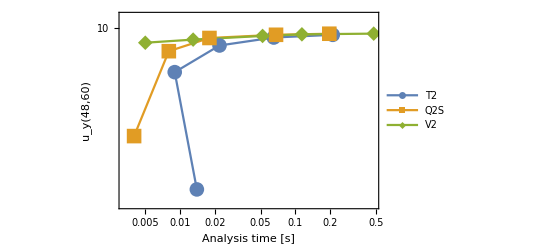

```mathematica
"Displacement of upper right edge over analysis time (time without mesh generation)";
legend={"T2","Q2S","V2"};
ListLogLogPlot[s1[[;;,;;,{5,3}]],Frame->True,FrameLabel->{Style["Analysis time [s]",15,Bold],Style["u_y(48,60)",15,Bold]},GridLines->Automatic,PlotLegends->Placed[LineLegend[legend,LegendFunction->(Framed[#,Background->White,RoundingRadius->5]&),LegendMargins->0,LabelStyle->{FontSize->13}],{{0.99,0.01},{0.99,0.01}}],GridLinesStyle->Dotted,FrameTicksStyle->Directive[15,Bold],PlotMarkers->{Automatic,15},FrameTicks->{Automatic,Automatic},ImageSize->400,PlotRange->{Automatic,{8.6,10.1}},Joined->True]
```

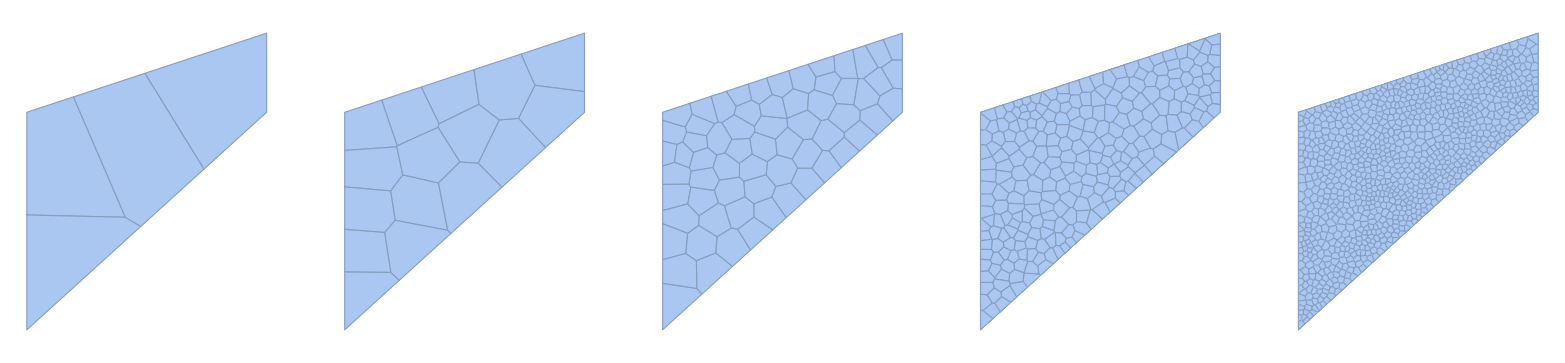

```mathematica
GraphicsRow[voroMeshes]
```

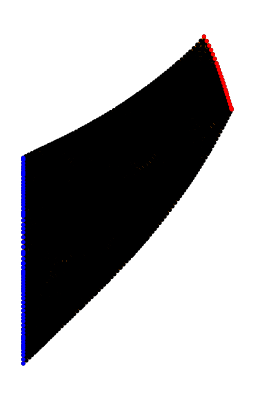

```mathematica
"Visualization";
xi=SMTNodeData["X"]+SMTNodeData["at"];
Elements=DeleteCases[#,SMTNoNodes+1]&/@SMTElementData["Nodes"];
displacements=SMTNodeData["at"][[;;,2]];
With[{dis=Rescale[displacements]},toColor[n_Integer]:=List@@ColorData["Rainbow",dis[[n]]];
SetAttributes[toColor,{Listable}]];
Show[Graphics[GraphicsComplex[xi,Polygon[Elements,VertexColors->toColor[Elements]]]],Graphics[{RGBColor[0.86,0.42,0.],Flatten[MeshPrimitives[#,1]&/@(Polygon[xi[[#]]]&/@Elements)]}],ListPlot[SMTNodeData["X"]+SMTNodeData["at"],PlotStyle->Directive[PointSize[Small],Black],Axes->False],ListPlot[(SMTNodeData["X"]+SMTNodeData["at"])[[SMTFindNodes["X"==0&]]],PlotStyle->Directive[PointSize[Medium],Blue],Axes->False],ListPlot[(SMTNodeData["X"]+SMTNodeData["at"])[[SMTFindNodes["X"==48&]]],PlotStyle->Directive[PointSize[Medium],Red],Axes->False]]
```

```mathematica
SMTSimulationReport[];
```

No. of nodes | 5123
No. of elements | 1024
No. of equations | 10108
Number of threads used/max | 12/12
Data memory (KBytes) | 7001
Tangent matrix (KBytes) | 1928
Solver memory (KBytes) | 31419
Total driver (KBytes) | 40348
MMA kernel memory (KBytes) | 236312
MMA front end memory(KBytes) | 755360
Total memory (KBytes) | 1032020
Solver type | Pardiso
Matrix type | -2
No. of steps | 1
No. of steps back | 0
Step efficiency (%) | 100.
Total no. of iterations | 7
Average iterations/step | 7.
Terminal BC multiplier (λ) | 1.
Terminal time (t) | 0.
Terminal parameter (γ) | 0. | Direct analysis: | 
Total absolute time (s) | 37.765
Total linear solver time (s) | 0.365
Total linear solver time (%) | 0.96652
Total K&R time (s) | 0.113
Total K&R time (%) | 0.29922
Average time/iteration (s) | 5.3927
Average linear solver time (s) | 0.052143
General timing: | 
Input data phase (s) | 0.48608
Input data phase (%) | 1.2871
Total visualization time (s) | 0
Total visualization time (%) | 0
Total driver time (s) | 37.749
CPU Mathematica time (s) | 3.344
CPU Mathematica time (%) | 8.8549 | {}

## Nonconvex shaped problem

```mathematica
"Due to trimming algorithm, the number of voronoi cells increases with a higher number of Lloyd iterations at sharp nonconvex edges";
```

```mathematica
"BVP description";
```

```mathematica
pts={{0.,0.},{2.,0.},{0.,-0.1},{0.,-1.},{3.,-1.},{3.,1.},{0.,1.}};
q={50,0};
μ=40;
λ=100;
Em=μ(3λ+2μ)/(λ+μ)//N;
ν=λ/(2(λ+μ))//N;
```

### Analysis

```mathematica
"Batch run";
s1=Table[
n=2^dd;

"Mesh generation";
Switch[ff
,1,DiscPoly[n^2,"Lloyd",5,pts];
,2,DiscPoly[3/n,"Honey",0,pts];];

"Initialization";
SMTInputData[];
SMTAddDomain["Ω","VEM2-NH-MF-X4",{"E *"->Em,"ν *"->ν,"βs *"->1.0}];
SMTAddMesh[allCoorPoly2,{"Ω"->nodOfPoly2}];
SMTAnalysis["NodeReordering"->False];
SMTTask["Initialization"];
(*"not needed here; no Neumann boundaries in this problem";
SMTTask["ClearNormals"];
SMTTask["GetNormals"];
normals=SMTNodeData["Data"][[;;,{1,2}]]//Chop;*)

"Dirichlet boundaries";
SMTAddEssentialBoundary["X"==0 &&"Y">=0&,1->0,2->0];
SMTAddEssentialBoundary["X"==0 &&"Y"<0&,2->-1];

"Solution procedure";
SMTEquilibriumPaths["Method"->"Newton","Steps"->"Adaptive","Show"->False,"λMax"->1,"Δλ0"->1,"ΔλMin"->1/1000,"ΔλMax"->1,"Tolerance"->10.^-12,"MaxIterations"->15,"OptimalIterations"->8];

"Visualization";
xi=SMTNodeData["X"]+SMTNodeData["at"];
Elements=DeleteCases[#,SMTNoNodes+1]&/@SMTElementData["Nodes"];
displacements=SMTNodeData["at"][[;;,2]];
With[{dis=Rescale[displacements]},toColor[n_Integer]:=List@@ColorData["Rainbow",dis[[n]]];
SetAttributes[toColor,{Listable}]];
GraphicsRow[{mesh,Show[Graphics[GraphicsComplex[xi,Polygon[Elements,VertexColors->toColor[Elements]]]],Graphics[{RGBColor[0.86,0.42,0.],Flatten[MeshPrimitives[#,1]&/@(Polygon[xi[[#]]]&/@Elements)]}],ListPlot[SMTNodeData["X"]+SMTNodeData["at"],PlotStyle->Directive[PointSize[Medium],Black],Axes->False],ListPlot[(SMTNodeData["X"]+SMTNodeData["at"])[[SMTFindNodes["X"==0&]]],PlotStyle->Directive[PointSize[Large],Blue],Axes->False],ListPlot[(SMTNodeData["X"]+SMTNodeData["at"])[[SMTFindNodes["X"==48&]]],PlotStyle->Directive[PointSize[Large],Red],Axes->False]]}]
,{ff,{1,2}},{dd,{3,4}}];
```

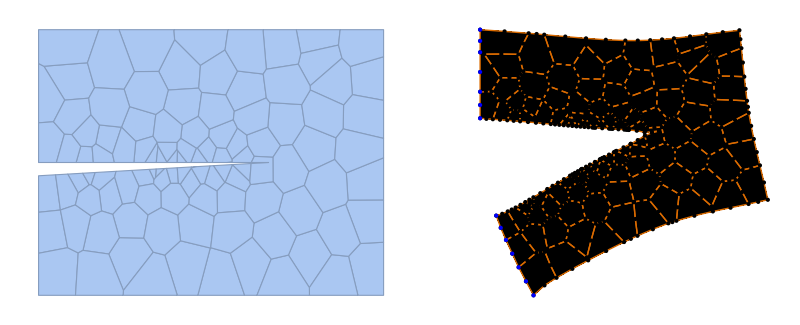
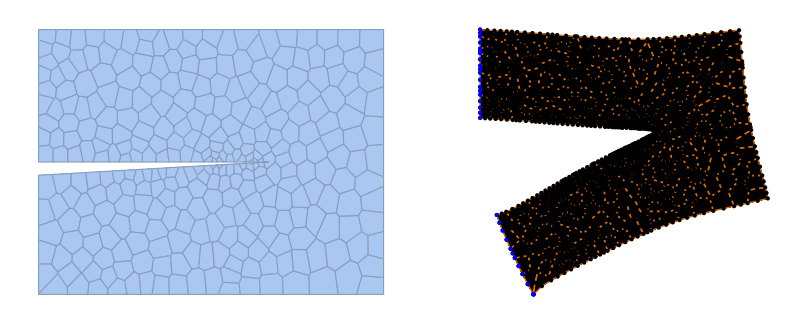
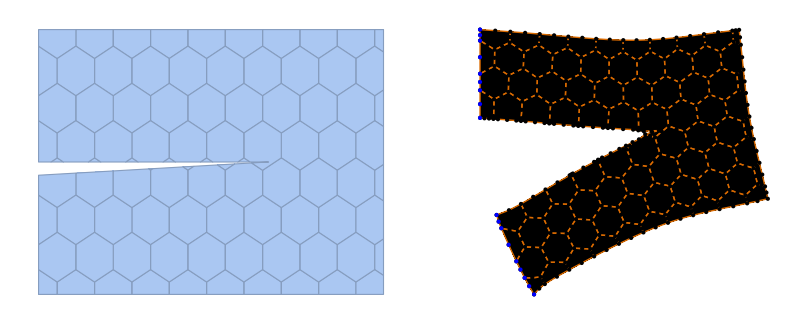
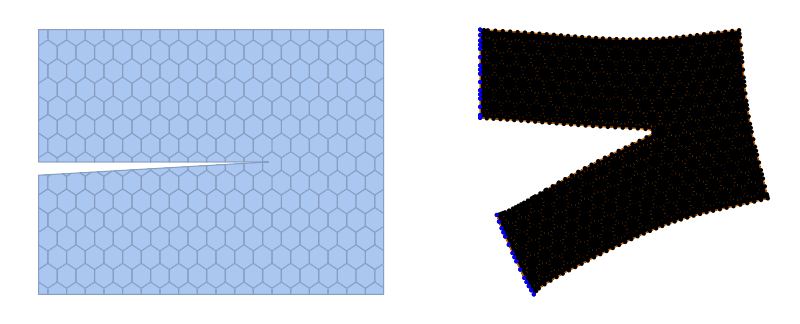

```mathematica
s1
```

```mathematica
SMTSimulationReport[];
```

No. of nodes | 1494
No. of elements | 297
No. of equations | 2939
Number of threads used/max | 12/12
Data memory (KBytes) | 2033
Tangent matrix (KBytes) | 521
Solver memory (KBytes) | 7948
Total driver (KBytes) | 10502
MMA kernel memory (KBytes) | 229835
MMA front end memory(KBytes) | 853582
Total memory (KBytes) | 1093919
Solver type | Pardiso
Matrix type | -2
No. of steps | 1
No. of steps back | 0
Step efficiency (%) | 100.
Total no. of iterations | 8
Average iterations/step | 8.
Terminal BC multiplier (λ) | 1.
Terminal time (t) | 0.
Terminal parameter (γ) | 0. | Direct analysis: | 
Total absolute time (s) | 6.9646
Total linear solver time (s) | 0.087
Total linear solver time (%) | 1.2492
Total K&R time (s) | 0.029
Total K&R time (%) | 0.41639
Average time/iteration (s) | 0.87057
Average linear solver time (s) | 0.010875
General timing: | 
Input data phase (s) | 0.23538
Input data phase (%) | 3.3797
Total visualization time (s) | 0
Total visualization time (%) | 0
Total driver time (s) | 6.9646
CPU Mathematica time (s) | 1.656
CPU Mathematica time (%) | 23.778 | {}